# Rough Work

#### Schw metric and computing limits

```mathematica
ClearAll["Global`*"]

r = rbar*(1 + M/(2*rbar))^2

FullSimplify[1-2*M/r]
```

(1+M/(2 rbar))^2 rbar

(M-2 rbar)^2/(M+2 rbar)^2

```mathematica
Clear[r]

M = 1

eq = r == rbar*(1 + M/(2*rbar))^2;

Solve[eq, rbar]
```

1

{{rbar→1/2 (-1+r-√(-2 r+r^2))},{rbar→1/2 (-1+r+√(-2 r+r^2))}}

```mathematica
rbarsolution = rbar /. Solve[eq, rbar][[2]]
```

1/2 (-1+r+√(-2 r+r^2))

```mathematica
Limit[rbarsolution/r, r -> Infinity]
```

1

```mathematica
roverrbar = (1 + M/(2*rbar))^2;

Limit[roverrbar, rbar-> Infinity]
```

1

Checking limit at horizon

```mathematica
rbarsolution /. r -> 2
```

1/2

In line with sarp.

#### TOV stuff

Now to convert the TOV metric to isotropic coords to compute the radial drop.

Solved the differential eqn below and by hand, by hand was better as it was copied from the paper.

```mathematica
eq = D[rbar[r], r] == rbar[r]/(r Sqrt[1 - k^2 r^2]);
FullSimplify[DSolve[eq, rbar, r]] (*Different answer given in paper which i also got*)
```

{{rbar→Function[{r},ⅇ^(-ArcTanh[√(1-k^2 r^2)]) C[1]]}}

General Integration and Differentiation checks

```mathematica
D[-Tanh[x]^2,x] (*Computing a derivative*)
```

-2 Sech[x]^2 Tanh[x]

```mathematica
eq = -1/(Cosh[x]^2 (1 - Tanh[x]^2))
Integrate[eq, x]
```

-Sech[x]^2/(1-Tanh[x]^2)

-x

Final eqn obtained for rbar, more on r on paper in my copy

```mathematica
eq = rbar == C * Sqrt[(1 - Sqrt[1-k^2 r^2])/(1 + Sqrt[1 + k^2 r^2])]
```

rbar==C √((1-√(1-k^2 r^2))/(1+√(1+k^2 r^2)))

#### START from here, all above is metrics and limits.... Doing the Radial drop in isotropic coords

first looking at time in schw coords outside to drop to the Radius of the star.

```mathematica
Clear["Global`*"]
R0 = 20; (*Initial Drop point*)
RStar = 4 ; (*Radius of the Star*)
```

Convert r = 4M and r = 20M to isotropic coords

```mathematica
rSchw[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2] (*Block says use this value of M then forget it*)

rBarSchw[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])]
```

(1+1/(2 rbar))^2 rbar

1/2 (-1+r+√(-2 r+r^2))

Finally converting to isotropic coords

```mathematica
rbar0 = rBarSchw[R0];
rbarStar = rBarSchw[RStar];
```

Defining the Isotropic metric components for external Schwarzschild spacetime

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2];
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))];
```

```mathematica
E0=α[rbar0];
0<E0<=1
Ut0=E0/α[rbar0]^2;
Utdrop[rbar_]=E0/α[rbar]^2;
Urdrop[rbar_]=-1/A[rbar] √(E0^2/α[rbar]^2-1);
```

True

Times:

```mathematica
tSchw[rbar_,rf_]:=Block[{M=1},-1/(√(2M))NIntegrate[(√(1-2M/rbar))/(√(1/r-1/rbar))1/(1-2 M/r),{r,rbar,rf}]];
(*from MTW book*)
```

```mathematica
tauSchw[RStart_, rFinish_] = Block[{M=1}, 1/Sqrt[2 M] (rFinish RStart Sqrt[1/rFinish - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/rFinish - 1]]) -(1/Sqrt[2 M] (RStart RStart Sqrt[1/RStart - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/RStart - 1]]))];
```

```mathematica
tauSchw[20, 4];
```

```mathematica
tauIsotropic[rStart_, rFinish_] :=NIntegrate[1/Urdrop[rBar],{rBar,rStart,rFinish},WorkingPrecision->40]
```

```mathematica
NumericQ@tauIsotropic[rbar0, rbarStar]
Print["Check proper time equality: ",Abs[1-tauSchw[20,4]/tauIsotropic[rbar0,rbarStar]]<10^-16] (*Correct up to here*)
```

True

Check proper time equality: True

#### Doing radial drop pretending to be an observer at infinity

```mathematica
Ut[rbar_,ur_]=1/α[rbar] √(1+ur^2/A[rbar]^2);
drBardt[rbar_, ur_] = 1/(A[rbar]^2 Ut[rbar, ur])ur;
durdt[rbar_, ur_] = -α[rbar] Ut[rbar, ur] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur]((Derivative[1][A][rbar])/A[rbar]^3);
```

not following 2M part of the notebook as we are dealing with a star, so rEnd = 4

```mathematica
t0 = 0;
rEnd=4;
rBarEnd = rBarSchw[rEnd];
tEnd = tSchw[R0, RStar];
sol  = NDSolve[{rbar'[t] == drBardt[rbar[t], ur[t]], ur'[t] == durdt[rbar[t], ur[t]],
rbar[0] == rbar0, ur[0] == 0}, {rbar, ur}, {t, t0, tEnd}][[1]]
```

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…]}

```mathematica
(*Extract Solutions and plot*)
rbarNum = rbar /. sol;
urNum = ur /. sol;
```

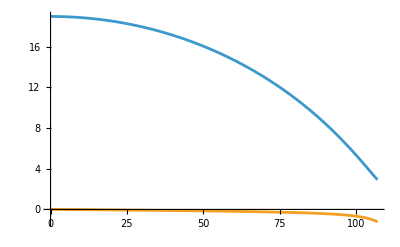

```mathematica
Plot[{rbarNum[t], urNum[t]}, {t, t0, tEnd}] (*rbarNum = blue, urNum = orange*)
```

#### Checking that the simple solution using the analytic integral and ND solving the ODES agree on the same proper time as a function of rbarFinal

```mathematica
tauNDSolve[tf_] := NIntegrate[α[rbarNum[t]]^2/E0, {t, t0, tf}];
```

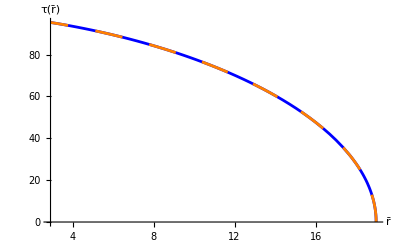

```mathematica
Show[Plot[tauIsotropic[rbar0,r],{r,rbar0,rbarStar},PlotStyle->Blue]
,ParametricPlot[{rbarNum[tf],tauNDSolve[tf]},{tf,t0,tEnd},PlotStyle->{Dashing[0.05],Orange}],AxesLabel->{"r̄","τ(r̄)"}]
```